```mathematica
(*frtr is the emittance reduction factor for the trapezium shape,the higher it is the better. It depends only on λ and ρ (see the contour below). It is  λ=L1/L2 and ρ=ρ1/ρ2, where L1 is the high field and L2 the low field length for the half dipole, ρ1 is the bending radius that corresponds to the maximum field at the dipole's center and ρ2 corresponds to the minimum field at the dipole's edge.*)
frtr=(4 √2 (1+ρ) (λ (-1+ρ)+ρ Log[ρ])^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))/((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2)
```

(4 √2 (1+ρ) (λ (-1+ρ)+ρ Log[ρ])^3 √(((-1+ρ)^3 (2+ρ+ρ^2) (-6 λ (-1+ρ)^2 ρ^2 (1+ρ)+3 ρ^3 (-1+ρ^2)+2 λ^2 (-1+ρ)^3 (2+3 ρ (1+ρ))+6 ρ^4 Log[ρ] (2 λ (-1+ρ)-ρ+ρ Log[ρ])))/((-1+ρ)^2 (-120 λ^3 (-1+ρ)^3 ρ^2 (1+ρ)+16 λ^4 (-1+ρ)^4 (1+3 ρ (1+ρ))+15 λ^2 (-1+ρ)^2 ρ^3 (20+3 (-1+ρ) ρ (3+ρ))+45 ρ^5 (-44+ρ (-3+(-6+ρ) ρ))+90 λ (-1+ρ) ρ^4 (-8+ρ (5+(-2+ρ) ρ)))-60 ρ^4 Log[ρ] (-2 (-1+ρ) (2 λ^3 (-1+ρ)^3-6 λ (-2+ρ) (-1+ρ) ρ-λ^2 (-1+ρ)^2 ρ+3 ρ (2+5 ρ))-3 (-2+ρ) ρ (λ (-1+ρ)+ρ)^2 Log[ρ]))))/((-1+ρ) (3 ρ^3 (1+ρ)-6 λ ρ^2 (-1+ρ^2)+2 λ^2 (-1+ρ)^2 (2+3 ρ+3 ρ^2))+6 (2 λ (-1+ρ)-ρ) ρ^4 Log[ρ]+6 ρ^5 Log[ρ]^2)

```mathematica
(*The frtr (Subscript[F, TME]) dependance on ρ and λ is shown in the contourplot below. The blue colored areas are the desired ones. Both ρ and λ vary between a min and a max value (here it is 0.1-1), of course if it is feasible to build such a magnet someone can go to min<0.1 !!! *)
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

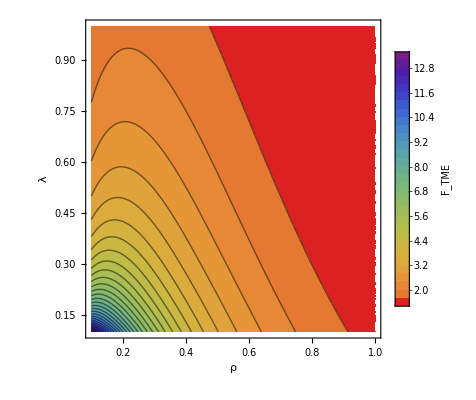

```mathematica
ContourPlot[(frtr),{ρ,0.1,1},{λ,0.1,1},Contours->30,PlotRange->All,ColorFunction->(ColorData["Rainbow"][1-#]&),PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[F, TME]],FrameLabel->{"ρ","λ"},LabelStyle->Directive[25],PlotPoints->50]
```

```mathematica
Nd=90; (*is total number of dipoles*)
Ld=0.58/2 ;(*is the half dipole length*)
ρ1=4.111; (*is the bending radius at the dipole's center that corresponds to the maximum field (Bmax=2.86/(0.299796139*ρ1))*)
```

```mathematica
(*for the frtrfix the number of dipoles, their length and max. field are fixed, so now λ depends only on ρ.*)
```

```mathematica
frtrfix=Simplify[frtr/.λ->-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))]
```

-((0.166867 (1.+ρ) (1.-1. ρ+1. ρ Log[ρ])^3 √(((-1.+ρ)^3 (2.+ρ+ρ^2) (-0.666667+1. ρ-1.02089 ρ^2+1.16645 ρ^3-0.979108 ρ^4+0.500218 ρ^5+ρ (-2.69452+1.34726 ρ-0.715852 ρ^2+2. ρ^3-0.979108 ρ^4) Log[ρ]+ρ^2 (-2.72267-1.36134 ρ+1. ρ^3) Log[ρ]^2))/(0.0835336-0.250601 ρ+0.639591 ρ^2-0.341245 ρ^3-0.0665817 ρ^4-14.259 ρ^5+28.6795 ρ^6-18.3921 ρ^7+7.93793 ρ^8-5.03101 ρ^9+1. ρ^10+ρ (0.67525-1.3505 ρ+2.52714 ρ^2-0.379727 ρ^3-4.09576 ρ^4-13.9926 ρ^5+19.2721 ρ^6-5.68687 ρ^7+5.03101 ρ^8-2. ρ^9) Log[ρ]+ρ^2 (2.04691-2.04691 ρ+1.69555 ρ^2+0.884332 ρ^3+2.43047 ρ^4-6.30211 ρ^5-0.729017 ρ^6+1. ρ^8) Log[ρ]^2+ρ^3 (2.75772-6.4472×10^-16 ρ-2.99441 ρ^2-0.281215 ρ^3+2.54777 ρ^4+2.01149 ρ^5) Log[ρ]^3+ρ^4 (1.39327+1.39327 ρ-2.78653 ρ^2-1.62228 ρ^3-2.37772 ρ^4) Log[ρ]^4)))/(-0.666667+1. ρ-1.02089 ρ^2+1.16645 ρ^3-0.979108 ρ^4+0.500218 ρ^5+ρ (-2.69452+1.34726 ρ-0.715852 ρ^2+2. ρ^3-0.979108 ρ^4) Log[ρ]+ρ^2 (-2.72267-1.36134 ρ+1. ρ^3) Log[ρ]^2))

```mathematica
frtr/.λ->0.0363/.ρ->1/(2.321/0.685)
```

7.09824

```mathematica
FindMaximum[frtr/.λ->-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1)),{ρ,0.2}]
```

{8.3514,{ρ→0.271438}}

```mathematica
FindMaximum[frtr/.λ->-(π ρ1-π ρ ρ1+100 Ld ρ Log[ρ])/((-1+ρ) (100 Ld-π ρ1)),{ρ,0.2}]
```

{10.7787,{ρ→0.228951}}

```mathematica
1/(2.32/0.68)
```

0.293103

```mathematica
}
```

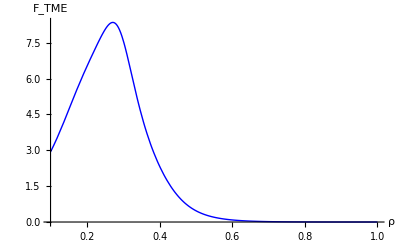

```mathematica
Plot[frtrfix,{ρ,0.1,1},PlotRange->All,AxesLabel->{"ρ","F_TME"},LabelStyle->Directive[25], PlotStyle->{Blue, Thick}]
```

```mathematica
rho=ρ/.Last[FindMaximum[frtrfix,{ρ,0.2}]] (*this is the optimal value for ρ*)
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.271329

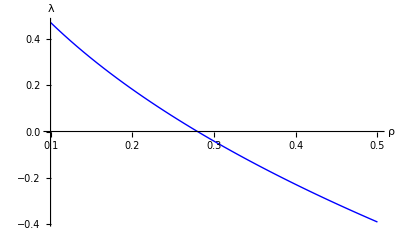

```mathematica
Plot[-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1)),{ρ,0.1,0.5},PlotRange->Automatic,AxesLabel->{"ρ","λ"},LabelStyle->Directive[25], PlotStyle->{Blue, Thick}]
```

```mathematica
lambda=-(π ρ1-π ρ ρ1+Nd Ld ρ Log[ρ])/((-1+ρ) (Nd Ld-π ρ1))/.ρ->rho(*this is the optimal value for λ, it always must be positive. So, if needed the ρ can be reduced(lower Subscript[F, TME]) so that to have a realistic value for λ*)
```

0.0180419

```mathematica
frtr/.λ->lambda/.ρ->rho
```

8.35139

```mathematica
2.86/(0.299796139*4.11)
```

2.32112

```mathematica
Bmax=2.86/(0.299796139*ρ1)
```

2.00838

```mathematica
BB=2.86/(0.299796139(((-Ld+L1 1/ρ+s-1/ρ s) ρ1)/(L1-Ld)))/.L1->Ld/(1+1/λ)/.λ->lambda/.ρ->rho (*the field evolution for the half dipole*)
```

-0.57041/(-0.272766-1.87942 s)

```mathematica
opBB=BB/.s->-s(*the field evolution for the other half of the dipole*)
```

-0.57041/(-0.272766+1.87942 s)

```mathematica
s1=Ld/(1+1/λ)/.λ->lambda(*the L1 length with the max. field*)

s2=Ld-s1/.λ->lambda/.ρ->rho(*the L2 length where the field decreases till it reaches the minimum*)
```

0.00598531

0.284015

```mathematica
shape11=Plot[BB,{s,s1,s2},PlotStyle->Thick,PlotRange->All];
shape22=Plot[opBB,{s,-s1,-s2},PlotStyle->Thick];
shape33=Plot[Bmax,{s,-s1,s1},PlotStyle->Thick];
```

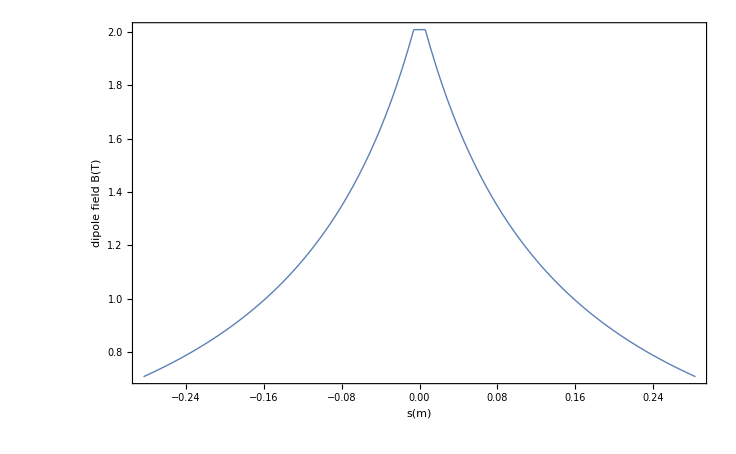

```mathematica
Show[{shape33,shape22,shape11},Frame->True,FrameLabel->{s[m] ,dipole field B[T]},FrameStyle->Directive[20],PlotRange->Automatic]
```